# :d83d:dcab Bset 1: Orientation and Particle Motion

```mathematica
SetDirectory@NotebookDirectory[];
<<"../MMA library.m"
```

## Reflection

This document lives in Mathematica, so reflection and notes are formatted green instead of my normal blue.

## Euler Angle Review

```mathematica
With[{context="s1`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

#### 1. What’s the Matrix?

```mathematica
yawMatrix=RotationMatrix[ψ,UnitVector[3,3]];
pitchMatrix=RotationMatrix[θ,UnitVector[3,2]];
rollMatrix=RotationMatrix[ϕ,UnitVector[3,1]];
```

```mathematica
rollMatrix.yawMatrix.pitchMatrix//MatrixForm
```

rollMatrix.yawMatrix.pitchMatrix

I’m not 100% solid about why this is “roll*pitch*yaw” instead of “pitch*yaw*roll”. Because the roll operation is applied last to the body, I want to multiply it first such that its effect isn’t affected by the other transformations (if that made any sense).

```mathematica
With[{context="s1`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Build a Gimbal

```mathematica
With[{context="gimbal`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

```mathematica
With[{context="gimbal`"},If[Context[]==context,End[],"Not in context"]]
```

## Gimbal Lock

### 8. What is gimbal lock?

Gimbal lock is a situation in which two points that are adjacent (or arbitrarily close) on a sphere have dramatically different representations as angles pointing to them. This usually (always?) occurs at singularities, like the poles of a pan-tilt-yaw coordinate system. When a system is in gimbal lock, moving a small amount in one direction requires coordinated and long motion of multiple axes, which can cause componentwise interpolation to fail. This is particularly challenging when dealing with a physical system in which the axes cannot reorient arbitrarily quickly or when dealing with an animation environment in which smooth interpolation is a critical feature of the system.

### 9. Find it.

In 3-1-3 Euler angles, gimbal lock occurs whenever the second rotation is 0. In this case, the first and third axes are collinear.

In 3-2-1 angles, gimbal lock occurs when the second rotation is ±90 degrees, because that again puts the first and third rings into parallel alignment.

## Particle Motion

I am a leaf on the wind. Watch how I soar.

```mathematica
With[{context="s4`"},If[Context[] ≠ context,Begin[context]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

As a result of being in Mathematica, some of the rote transformation steps aren’t necessary for me to solve these types of problems (particularly converting second-order vector DE’s to first-order scalar DE’s). I know how to do them, but won’t be doing so unless actually necessary.

For any others wondering how I made this work with vector equations, note that I defined my forces as functions that only evaluate when fed a list of numbers. This prevents things from simplifying incorrectly before they should.

```mathematica
ClearAll@windyLeaf
windyLeaf[wind_]:=
Module[{x,t,fg, fd,distance,end,simRange,diffeqs,events,initialConditions},

(* Setup initial conditions *)
initialConditions={x[0]=={0,0,0},x'[0]==QuantityMagnitude@UnitConvert[Quantity[130, ("Miles")/("Hours")],Quantity[, ("Meters")/("Seconds")]]{0,1/Sqrt@2,1/Sqrt@2}};

With[
(* Setup parameters *)
{w=wind,m=0.05,g=9.8,cd=.25,d=4.27/100,ρ=1.29},

(* define forces as function of velocity *)
ClearAll[fg, fd];
fg[v_?(VectorQ[#]&)]:={0,0,-m g};fd[v_?(VectorQ[#]&)]:=(-1/2 ρ cd (Pi d^2/4)Norm[v-w](v-w));

simRange={t,0,Infinity};

diffeqs={(fg[x'[t]]+fd[x'[t]]==m x''[t])};
events={WhenEvent[x[t][[3]]==0,
end=t;
distance=Norm[x[t]];
"StopIntegration"]};
]

sol=NDSolveValue[Join[initialConditions,diffeqs,events],x[t],simRange];
Column[{
Join[initialConditions,diffeqs] // TraditionalForm;

Row[{"Distance travelled: ",distance," meters"}],

ParametricPlot3D[sol,{t,0,end},PlotLegends->{"projectile path"},AxesLabel->{"x","y","z"},PlotRange->Full,ImageSize->Medium],
With[{dsol=sol[[0]]'[t]},

Plot[{sol[[1]],sol[[2]],sol[[3]],dsol[[1]],dsol[[2]],dsol[[3]]},{t,0,end},PlotLegends->{"x","y","z","x'","y'","z'"},ImageSize->Medium]]},
Frame->All,Alignment->Center]
]
```

### Results with no wind:

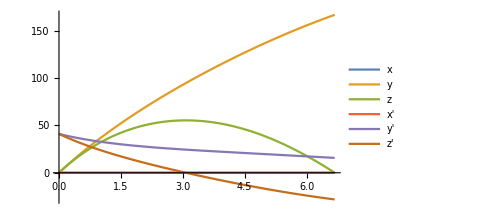
Distance travelled: 167.014 meters
-Graphics3D-
-Graphics-

```mathematica
windyLeaf[{0,0,0}]
```

### Results with an extreme tail wind

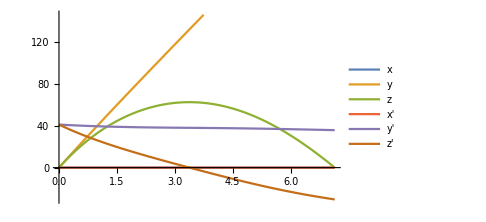
Distance travelled: 271.217 meters
-Graphics3D-
-Graphics-

```mathematica
windyLeaf[{0,30,0}]
```

### Results with an extreme headwind

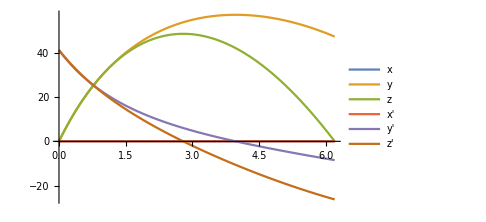
Distance travelled: 47.1504 meters
-Graphics3D-
-Graphics-

```mathematica
windyLeaf[{0,-30,0}]
```

### Results with headwind and crosswind

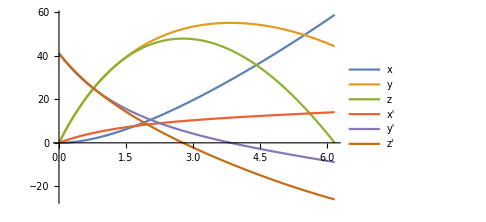
Distance travelled: 73.6063 meters
-Graphics3D-
-Graphics-

```mathematica
windyLeaf[{20,-30,0}]
```

### Results with strong updraft and tailwind

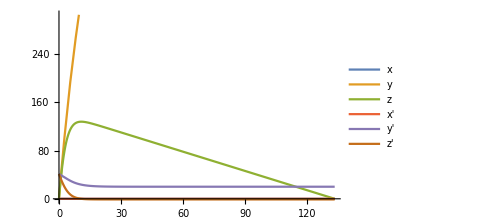
Distance travelled: 2797.81 meters
-Graphics3D-
-Graphics-

```mathematica
windyLeaf[{0,20,45}]
```

### Results with extreme updraft

```mathematica
windyLeaf[{0,0,70}]
```

NDSolveValue::evcvmit: Event location failed to converge to the requested accuracy or precision within 100 iterations between t$149645 = 1.20099×10^55 and t$149645 = 1.65136×10^55.

Distance travelled: 2.78642×10^81 meters
-Graphics3D-
-Graphics-

```mathematica
With[{context="s4`"},If[Context[]==context,End[]]];Dynamic[Refresh[Context[],UpdateInterval->1]]
```

## Scratch Work

```mathematica
{1,2,3}-{1,3,5}
```

{0,-1,-2}

```mathematica
Unique[][t]
```

$82[t]

```mathematica
ClearAll@var
rhs[_?(NumberQ[#] &)]:=var[t]-{1,2};
rhs[x]/.x->{1,2}
```

{-1+var[t],-2+var[t]}

```mathematica
VectorQ@var
```

False

```mathematica
ClearAll[x,t]

(* Setup initial conditions *)
initialConditions={x[0]=={0,0,0},x'[0]==QuantityMagnitude@UnitConvert[Quantity[130, ("Miles")/("Hours")],Quantity[, ("Meters")/("Seconds")]]{0,1/Sqrt@2,1/Sqrt@2}};

With[
(* Setup parameters *)
{w={100,0,0},m=0.05,g=9.8,cd=.25,d=4.27/100,ρ=1.29},

(* define forces as function of velocity *)
ClearAll[fg, fd];
fg[v_?(VectorQ[#]&)]:={0,0,-m g}/.params;fd[v_?(VectorQ[#]&)]:=(-1/2 ρ cd (Pi d^2/4)(v-w))/.params;

simRange={t,0,Infinity};

diffeqs={(fg[x'[t]]+fd[x'[t]]==m x''[t])}/.params;
events={WhenEvent[x[t][[3]]==0,
end=t;
distance=Norm[x[t]];
"StopIntegration"]};
]
Join[initialConditions,diffeqs] // TraditionalForm
```

{x(0)=={0,0,0},x'(0)=={0,(18161 √2)/625,(18161 √2)/625},fd(x'(t))+fg(x'(t))==0.05 x''(t)}

InterpolatingFunction[{{0., 8.33301}}, <>][t]

336.301

-Graphics3D-

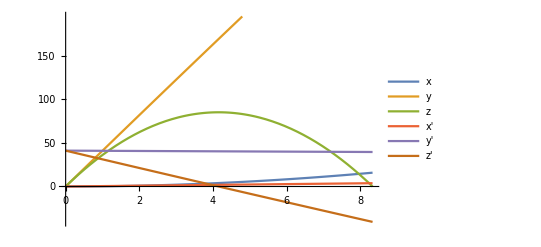

InterpolatingFunction[{{0., 8.33301}}, <>][t]

```mathematica
sol=NDSolveValue[Join[initialConditions,diffeqs,events],x[t],simRange]
distance
ParametricPlot3D[sol,{t,0,end},PlotLegends->{"projectile path"},AxesLabel->{"x","y","z"},PlotRange->Full]
With[{dsol=sol[[0]]'[t]},
Plot[{sol[[1]],sol[[2]],sol[[3]],dsol[[1]],dsol[[2]],dsol[[3]]},{t,0,end},PlotLegends->{"x","y","z","x'","y'","z'"}]]
```